## ArXiv: 2205.12373 [hep-th]

### The model

AF5/τ^4+AO3/τ^3+AF3/(s τ^3)+(AH3 s)/τ^3+AD5/(√s τ^(5/2))

_______________________________________________________ taur = 10

min = {0.09263953074,{s→1.191896944,τ→2.694633267,AF3→-0.1168842545,AH3→0.1214243305,AO3→-0.9588118579,AF5→1.105686359,AD5→0.3337492431}}

diV = {-0.0003482170306,-0.003023689464}

m^2 = {0.00602247337,0.0120879719}

_______________________________________________________ taur = 20

min = {0,{s→1.706633032,τ→3.341795305,AF3→1.03882196,AH3→0.4775980405,AO3→-1.565123564,AF5→-0.5078798402,AD5→0.294981161}}

diV = {9.76853711×10^-24,4.162654947×10^-24}

m^2 = {-0.002710657879,0.01406195133}

_______________________________________________________ taur = 30

min = {0.01966250235,{s→1.995679667,τ→2.822428324,AF3→-0.5782039604,AH3→-0.04140913133,AO3→-0.4160390299,AF5→0.8896020446,AD5→0.3979177465}}

diV = {-0.0006578837636,-0.001238321117}

m^2 = {-0.002514446003,0.005498390439}

_______________________________________________________ taur = 40

min = {0,{s→1.767386054,τ→1.261093653,AF3→-0.4400430895,AH3→0.1436700669,AO3→-1.378125914,AF5→0.5060310865,AD5→1.190703812}}

diV = {1.681958711×10^-20,1.230707503×10^-20}

m^2 = {0.009226040685,0.1407430012}

_______________________________________________________ taur = 50

min = {0,{s→0.8228357744,τ→2.910736733,AF3→-0.117850976,AH3→0.2136816527,AO3→-0.6573583876,AF5→0.2030421625,AD5→0.3392690728}}

diV = {3.243378809×10^-24,-9.470679557×10^-24}

m^2 = {-0.002985454065,0.01200998549}

_______________________________________________________ taur = 60

min = {0,{s→1.893351497,τ→3.000715669,AF3→0.2643558289,AH3→0.1061375107,AO3→-0.3944457244,AF5→-0.1088219356,AD5→0.09743682697}}

diV = {1.425047683×10^-21,1.025990218×10^-21}

m^2 = {-0.001234363903,0.003840741506}

_______________________________________________________ taur = 70

min = {0,{s→2.204291561,τ→4.135422502,AF3→0.9930701194,AH3→0.2681078113,AO3→-0.7691296466,AF5→-1.570922928,AD5→0.2051122352}}

diV = {5.962218324×10^-24,3.616297851×10^-24}

m^2 = {-0.001549140977,0.003237713354}

_______________________________________________________ taur = 80

min = {0,{s→1.92349613,τ→4.061916657,AF3→0.2414110635,AH3→0.2070107247,AO3→-1.193546303,AF5→0.6561793551,AD5→0.3752840824}}

diV = {9.302366866×10^-24,2.005971327×10^-24}

m^2 = {-0.00005705619821,0.002686811039}

_______________________________________________________ taur = 90

min = {0,{s→0.9436885666,τ→2.637198855,AF3→-0.04799842245,AH3→0.3210259385,AO3→-1.016575153,AF5→0.3457448548,AD5→0.4232961566}}

diV = {8.588682565×10^-25,-2.610896308×10^-25}

m^2 = {-0.003330643978,0.0267716443}

_______________________________________________________ taur = 100

min = {0,{s→1.848201676,τ→4.219614384,AF3→-0.8671189283,AH3→0.1448129143,AO3→-1.50755216,AF5→1.522405981,AD5→0.9752708869}}

diV = {-7.135608102×10^-24,4.897117407×10^-24}

m^2 = {-0.000611492397,0.0009635901717}

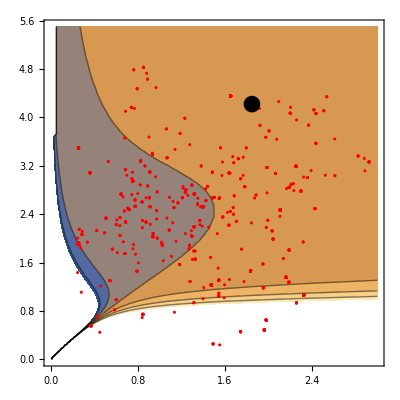

```mathematica
changmoduli=({τ->E^-ϕ vol^(1/2),ρ->vol^(1/3)}/.{vol ->(τ Exp[ϕ])^(3/2)});
VH3=(AH3 Exp[2ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VO3=AO3 PowerExpand[(ρ^((q-6)/2)τ^-3)/.changmoduli]/.{ϕ->Log[1/s]}/.{q->3};
VF5=AF5 PowerExpand[(ρ^(3-p)τ^-4)/.changmoduli]/.{ϕ->Log[1/s]}/.{p->5};
VF3=(AF3 Exp[4 ϕ])/ρ^6/.changmoduli/.{ϕ->Log[1/s]};
VR6=AR6 PowerExpand[(ρ^-1 τ^-2)/.changmoduli];
VD5=AD5/(√s τ^(5/2));
Vreal=VH3+VF3+0VR6+VD5+VF5+VO3
var={s,τ};
NM=Length[var];
mij=Simplify[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,NM},{j,1,NM}]];
detmij=Det[mij];
trmij=Tr[mij];
diV=Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]];
egval=Eigenvalues[Table[D[Vreal,var⟦i⟧,var⟦j⟧],{i,1,2},{j,1,2}]];
pfun=Function[{s,τ},10^4 If[egval⟦1⟧<0,egval⟦1⟧,0]+10^4 If[egval⟦2⟧<0,egval⟦2⟧,0]];
SetOptions[NMinimize,MaxIterations->500,WorkingPrecision->40];
max=100;
data=Table[0,{i,1,max}];
Do[
{min,steps}=Reap[
NMinimize[
{10^4 diV.diV+ 10^4(Abs[Vreal]-Vreal)+ 10^5(Abs[detmij-trmij^2/4]+detmij-trmij^2/4)+10^5(Abs[trmij]-trmij)+10^3(Abs[AD5]-AD5),s>RandomInteger[{1,100}]/100,τ>RandomInteger[{1,100}]/100},{s,τ,AF3,AH3,AO3,AF5,AD5},
Method->{"SimulatedAnnealing","PerturbationScale"->0.5,"LevelIterations"->50,"RandomSeed"->0,"PostProcess"->{FindMinimum,Method->"ConjugateGradient",MaxIterations-> 500,PrecisionGoal->10^2,WorkingPrecision->500}},
StepMonitor:>Sow[{s,τ,AF3,AH3,AO3,AF5,AF1}]]];
ll=Length[steps⟦1⟧];
pp=Table[{steps⟦1⟧⟦i⟧⟦1⟧,steps⟦1⟧⟦i⟧⟦2⟧},{i,1,ll}];
If[Mod[taur,10]==0,
Print["_______________________________________________________ taur = ",taur];
Print["min = ",N[min,10]];
Print["diV = ",N[Simplify[Table[D[Vreal,var⟦i⟧],{i,1,NM}]]/.min⟦2⟧,10]];
Print["m^2 = ",N[egval/.min⟦2⟧,10]];
];
data⟦taur⟧=Flatten[N[{min⟦1⟧,min⟦2⟧,egval/.min⟦2⟧},10]];
,{taur,1,max}]
Show[ContourPlot[Vreal/.min⟦2⟧⟦;;⟧,{s,0,3},{τ,0,5.5},Epilog->{PointSize[.03],Point[{s,τ}/.min⟦2⟧]}],ListPlot[pp,PlotStyle->Red]]
```

87

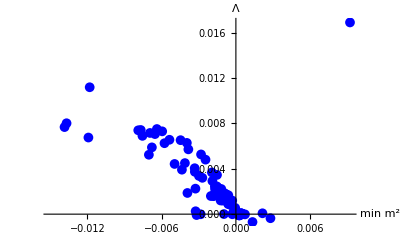

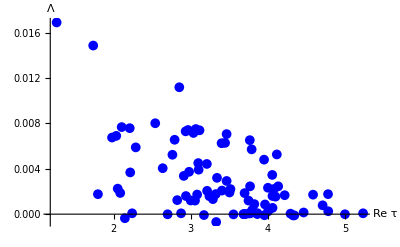
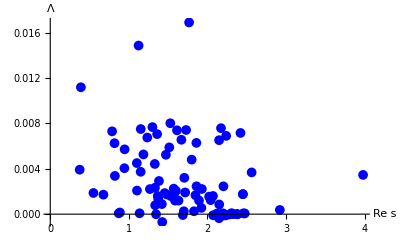

```mathematica
SetOptions[FindRoot,MaxIterations-> 500,Compiled->False,WorkingPrecision->1000,Method-> Automatic];
$MaxExtraPrecision=10000;
max=Length[data];
datag=Table[0,{i,max}];
up=Length[data⟦1⟧]-2;
Do[
fr=Quiet@FindRoot[diV/.data⟦jj⟧⟦4;;up⟧,{{s,s/.data⟦jj⟧⟦2⟧},{τ,τ/.data⟦jj⟧⟦3⟧}}];
If[Min[Re[diV/.data⟦jj⟧⟦4;;up⟧/.fr]]==0.0,
datag[[jj]]=N[Flatten[{Vreal/.fr/.data⟦jj⟧⟦4;;up⟧,fr,data⟦jj⟧⟦4;;up⟧,egval/.fr/.data⟦jj⟧⟦4;;up⟧}],30];
];
,{jj,1,Length[data]}];
datag=DeleteCases[N[datag,5],0];
Length[datag]
f0=ListPlot[Table[{Min[data⟦i⟧⟦up+1;;up+2⟧],data⟦i⟧⟦1⟧},{i,Length[data]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Red];
f1=ListPlot[Table[{Min[datag⟦i⟧⟦up+1;;up+2⟧],datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" min m^2","Λ"},PlotStyle-> Blue];
Show[f1]
{ListPlot[Table[{τ/.datag⟦i⟧⟦3⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re τ","Λ"},PlotStyle-> Blue],ListPlot[Table[{s/.datag⟦i⟧⟦2⟧,datag⟦i⟧⟦1⟧},{i,Length[datag]}],BaseStyle->{FontSize->20},PlotMarkers->{"●",10},AxesLabel->{" Re s","Λ"},PlotStyle-> Blue]}
```

```mathematica
Print["Stable dS"];
up=Length[datag⟦1⟧]-2;
aux1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
Print["dS ",Length[aux1],". And the % dS is ",N@Length[aux1]/Length[datag] 100];
aux11=Table[If[ii==1,{"i","min V","m^2","m^2","s","τ","AF3","AH3","AF5","AO3","AF1"},
Flatten[{ii,aux1⟦ii⟧⟦2;;4⟧,Flatten[{s,τ,AF3,AH3,AF5,AO3,AF1}/.aux1⟦ii⟧⟦5;;⟧]}]],{ii,Length[aux1]}];
Grid[N[aux11,4], Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
Print["Stable AdS"];
aux2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,{jj,datag⟦jj⟧⟦1⟧,datag⟦jj⟧⟦up+1⟧,datag⟦jj⟧⟦up+2⟧,datag⟦jj⟧⟦2;;up⟧}],{jj,1,Length[datag]}],Null];
aux22=Table[If[ii==1,{"min V","m^2","m^2","s","τ","AF3","AH3","AF5","AO3","AD5"},
Flatten[{aux2⟦ii⟧⟦2;;4⟧,Flatten[{s,τ,AF3,AH3,AF5,AO3,AF1}/.aux2⟦ii⟧⟦5;;⟧]}]],{ii,Length[aux2]}];
Print["dS ",Length[aux2],". And the % of AdS is ",N@Length[aux2]/Length[datag] 100];
Grid[aux22, Alignment->Left,Spacings->{2,1},Frame->All,ItemStyle->"Text"]
```

Stable dS

dS 7. And the % dS is 8.04598

i | min V | m^2 | m^2 | s | τ | AF3 | AH3 | AF5 | AO3 | AF1
2. | 0.00006343 | 0.0004641 | 0.003211 | 2.475 | 3.753 | 0.7729 | 0.2357 | 0.9799 | -1.696 | AF1
3. | 0.0000422 | 0.0001493 | 0.003398 | 2.119 | 4.296 | 0.999 | 0.3059 | 0.7165 | -1.637 | AF1
4. | 0.01689 | 0.009226 | 0.1407 | 1.767 | 1.261 | -0.44 | 0.1437 | 0.506 | -1.378 | AF1
5. | 0.00008589 | 0.0003734 | 0.003458 | 2.308 | 3.866 | 0.7577 | 0.2581 | 0.9764 | -1.707 | AF1
6. | 0.00007471 | 0.00008921 | 0.001066 | 2.199 | 2.876 | 0.08915 | 0.03072 | 0.06231 | -0.182 | AF1
7. | 0.00007126 | 0.0004445 | 0.003218 | 2.457 | 3.773 | 0.7713 | 0.2382 | 0.9795 | -1.697 | AF1

Stable AdS

dS 9. And the % of AdS is 10.3448

min V | m^2 | m^2 | s | τ | AF3 | AH3 | AF5 | AO3 | AD5
-0.000019461 | 0.00073481 | 0.0019705 | 2.2878 | 3.5554 | -0.18521 | 0.12823 | 1.3402 | -1.3389 | AF1
-0.00069259 | 0.0013445 | 0.0032473 | 1.4256 | 3.3313 | -0.11688 | 0.12142 | 1.1057 | -0.95881 | AF1
-0.00010914 | 0.00026521 | 0.0025059 | 2.2064 | 4.3448 | 0.75206 | 0.24985 | 1.0308 | -1.5591 | AF1
-0.00010919 | 0.00027053 | 0.0024603 | 2.2346 | 4.3286 | 0.75482 | 0.24588 | 1.0313 | -1.5577 | AF1
-0.00035856 | 0.0027954 | 0.016803 | 2.1482 | 2.1465 | 0.72988 | 0.18489 | 0.14609 | -0.92338 | AF1
-0.0000951 | 0.00032272 | 0.0051765 | 2.0736 | 3.957 | 1.1715 | 0.35209 | 0.72329 | -1.8139 | AF1
-1.973×10^-7 | 0.0005547 | 0.0036944 | 2.3796 | 3.6867 | 0.76427 | 0.24635 | 0.97718 | -1.7025 | AF1
-5.58×10^-8 | 0.00055231 | 0.0037095 | 2.3732 | 3.6892 | 0.76375 | 0.24719 | 0.97705 | -1.703 | AF1

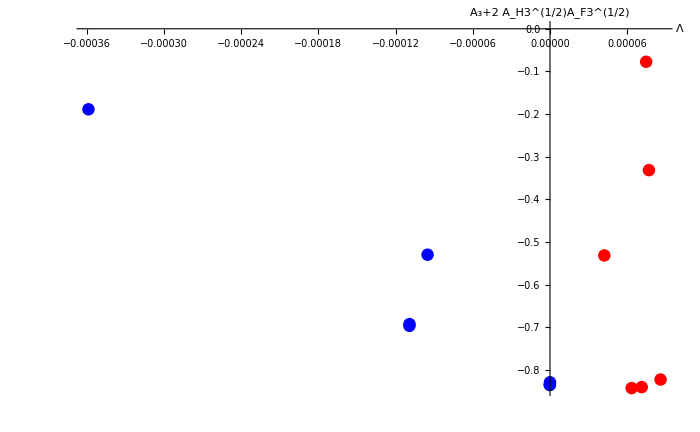

```mathematica
up=Length[datag⟦1⟧]-2;
datag1=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧>0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
datag2=DeleteCases[Table[If[datag⟦jj⟧⟦1⟧<0.0&&Min[datag⟦jj⟧⟦up+1;;up+2⟧]>0.0,datag⟦jj⟧⟦;;⟧],{jj,1,Length[datag]}],Null];
l1=Table[{datag1⟦jj⟧⟦1⟧,(AO3+2 AH3^(1/2)AF3^(1/2))/.datag1⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag1]}];
l2=Table[{datag2⟦jj⟧⟦1⟧,(AO3+2 AH3^(1/2)AF3^(1/2))/.datag2⟦jj⟧⟦2;;up⟧},{jj,1,Length[datag2]}];
f1=ListPlot[{l1,l2},PlotStyle->{Red,Blue},BaseStyle->{FontSize->20},AxesLabel->{"Λ","A_3+2 A_H3^(1/2)A_F3^(1/2)"},ImageSize->700]
```

values = {0.000076855,s→1.1371,τ→2.2404,AF3→0.023054,AH3→0.10404,AO3→-0.4292,AF5→0.21381,AD5→0.13967,0.0021488,0.013172}

AdS: Exact solution: {0.47074,0.8606}vs numerical sol: {s→0.47074,τ→0.8607}

dS: Exact solution: {1.137128575,2.24051423} vs numerical sol: {s→1.1371,τ→2.2404}

diV = {0.,0.} -> {0.,0.}

{s→0.47074,τ→0.8607}->{s→1.1371,τ→2.2404}

{2.1,0.693}->{0.0021488,0.013172}

V = -0.13-> V = 0.000076855

dS Vacua

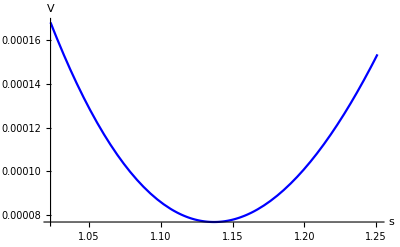
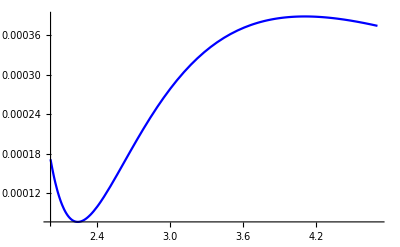

AdS Vacua

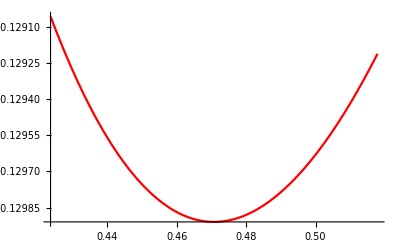
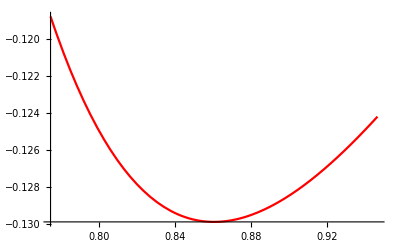

```mathematica
inter=aux1⟦1⟧⟦1⟧;
Print["values = ",datag⟦inter⟧];
Vold=Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧;
eqs=Table[D[Vold,var⟦i⟧],{i,1,2}];
sol=Quiet@Solve[Thread[%==0],var]⟦2⟧;
Print["AdS: Exact solution: ",{(AF3/AH3)^(1/2),(-4/3)AF5/(AO3+2 AH3^(1/2)AF3^(1/2))}/.datag⟦inter⟧⟦4;;up⟧,"vs numerical sol: ",sol];
(*******************************************)
poly=(Expand[-2 AF3^3+3 AF3^2 AO3 s+(AD5^2 AF5+12 AF3^2 AH3) s^2-6 AF3 AH3 AO3 s^3-18 AF3 AH3^2 s^4+3 AH3^2 AO3 s^5+8 AH3^3 s^6]);
auxsols=N[NSolve[(poly/.Rationalize[datag⟦inter⟧⟦4;;8⟧,10^-100])==0,s,WorkingPrecision->10]⟦5⟧,30];
Print["dS: Exact solution: ",{s/.auxsols,(4(-AF3+AH3 s^2)^2)/(AD5^2 s)/.Rationalize[datag⟦inter⟧⟦4;;8⟧,10^-100]/.auxsols}," vs numerical sol: ",datag⟦inter⟧⟦2;;3⟧];
(*******************************************)
Print["diV = ",diV/.datag⟦inter⟧⟦2;;up⟧," -> ",diV/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol]
Print[sol,"->",datag⟦inter⟧⟦2;;3⟧];
Print[Eigenvalues[mij/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol],"->",datag⟦inter⟧⟦up+1;;up+2⟧];
Print["V = ",Vold/.sol,"-> V = ",datag⟦inter⟧⟦1⟧];
Print["dS Vacua "];
{fo=Plot[Vreal/.datag⟦inter⟧⟦3;;up⟧,{s,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(s/.datag⟦inter⟧⟦2;;up⟧)]1.1},AxesLabel->{"s","V"},PlotStyle->Blue,ImageSize->{300}],
foτ=Plot[Vreal/.datag⟦inter⟧⟦2⟧/.datag⟦inter⟧⟦4;;up⟧,{τ,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)] 0.9,Evaluate[(τ/.datag⟦inter⟧⟦2;;up⟧)]2.1},PlotStyle->Blue,BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{300}]}
Print["AdS Vacua"];
{fn=Plot[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦2⟧,{s,Evaluate[(s/.sol⟦1⟧)] 0.9,Evaluate[(s/.sol⟦1⟧)]1.1},PlotStyle->Red,ImageSize->{300},BaseStyle->{FontSize->20,FontFamily->"Times"}],
Plot[Vreal/.{AD5->0}/.datag⟦inter⟧⟦4;;up⟧/.sol⟦1⟧,{τ,Evaluate[(τ/.sol⟦2⟧)] 0.9,Evaluate[(τ/.sol⟦2⟧)]1.1},PlotStyle->Red,BaseStyle->{FontSize->20,FontFamily->"Times"},ImageSize->{300}]}
```